## Ome Trem

```mathematica
oneTerm:=Block[{m,n,α,β},
{m,n}=RandomInteger[{-6,6},2];
{α,β}=Rationalize[RandomReal[{-π,π},2],1/1000];
{m Cos[n x+α]Cos[m y+β],n Sin[n x+α]Sin[m y+β]}
];
uv=Sum[oneTerm,{6}]
```

{-5 Cos[59/22+3 x] Cos[71/53-5 y]-4 Cos[25/18+3 x] Cos[9/14-4 y]-3 Cos[49/37+4 x] Cos[23/25-3 y]-3 Cos[25/28-6 x] Cos[45/17-3 y]-6 Cos[82/35] Cos[12/43+6 y]-6 Cos[43/14+5 x] Cos[37/22+6 y],3 Sin[59/22+3 x] Sin[71/53-5 y]+3 Sin[25/18+3 x] Sin[9/14-4 y]+4 Sin[49/37+4 x] Sin[23/25-3 y]-6 Sin[25/28-6 x] Sin[45/17-3 y]-5 Sin[43/14+5 x] Sin[37/22+6 y]}

## Analysis

```mathematica
ToExpression@Import["~/tmp/ss.txt"];
ds=ParallelMap[Partition[#,Sqrt@Length@#]&,Import["~/tmp/tmp.csv"]];
n=Length@ds⟦1,1⟧;
```

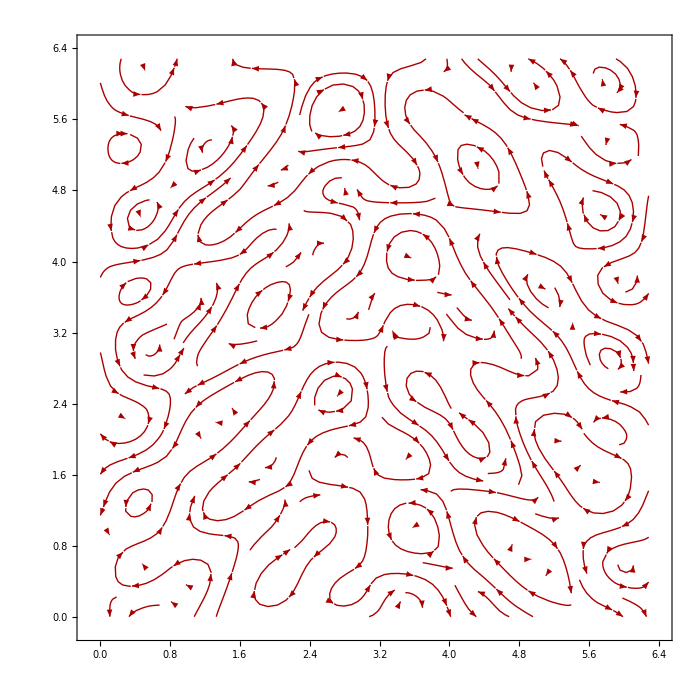

```mathematica
gs=StreamPlot[{u,v},{x,0,2π},{y,0,2π},StreamPoints->3000,PlotRangePadding->None,StreamStyle->Darker[Red],ImageSize->700,VectorStyle->Arrowheads[0]]
```

```mathematica
Manipulate[Show[ReliefPlot[ds⟦i⟧ᵀ,PlotRange->MinMax[ds],DataRange->{{0,2π},{0,2π}}],gs,PlotRange->{{0,2π},{0,2π}},ImageSize->700],{i,1,Length@ds,1}]
```

```mathematica
Dimensions@ds
```

{300,300,300}